```mathematica
-
```

# Manipolatore di Standford

## Cinematica diretta 3DOF

```mathematica
tab={{Subscript[q, 1],Subscript[L, 1],-Pi/2,0},{Subscript[q, 2],Subscript[L, 2],Pi/2,0},{0,Subscript[q, 3],0,0}};
TableForm[tab,TableHeadings->{{"1","2","3"},{"θ","d","α","a"}}]
```

| θ | d | α | a
1 | q_1 | L_1 | -π/2 | 0
2 | q_2 | L_2 | π/2 | 0
3 | 0 | q_3 | 0 | 0

```mathematica
Q03=cinematicaDiretta[tab];
h03=Q03[[1;;3,4]];
Q03/.{Cos[Subscript[q, i_]]->Subscript[c, i],Sin[Subscript[q, i_]]->Subscript[s, i]}//MatrixForm
```

(c_1 c_2 | -s_1 | c_1 s_2 | -L_2 s_1+c_1 q_3 s_2
c_2 s_1 | c_1 | s_1 s_2 | c_1 L_2+q_3 s_1 s_2
-s_2 | 0 | c_2 | L_1+c_2 q_3
0 | 0 | 0 | 1)

## Cinematica diretta 6DOF

```mathematica
tab2={{Subscript[q, 1],Subscript[L, 1],-Pi/2,0},{Subscript[q, 2],Subscript[L, 2],Pi/2,0},{0,Subscript[q, 3],0,0},{Subscript[q, 4],Subscript[L, 4],-Pi/2,0},{Subscript[q, 5],0,Pi/2,0},{Subscript[q, 6],Subscript[L, 6],0,0}};
tab2//MatrixForm
```

(q_1 | L_1 | -π/2 | 0
q_2 | L_2 | π/2 | 0
0 | q_3 | 0 | 0
q_4 | L_4 | -π/2 | 0
q_5 | 0 | π/2 | 0
q_6 | L_6 | 0 | 0)

```mathematica
cinematicaDiretta[tab2]/.{Cos[Subscript[q, i_]]->Subscript[c, i],Sin[Subscript[q, i_]]->Subscript[s, i]}//MatrixForm
```

(-s_1 (c_5 c_6 s_4+c_4 s_6)+c_1 (-c_6 s_2 s_5+c_2 (c_4 c_5 c_6-s_4 s_6)) | -c_6 (c_4 s_1+c_1 c_2 s_4)+(c_5 s_1 s_4+c_1 (-c_2 c_4 c_5+s_2 s_5)) s_6 | -s_1 s_4 s_5+c_1 (c_5 s_2+c_2 c_4 s_5) | c_1 ((L_4+c_5 L_6+q_3) s_2+c_2 c_4 L_6 s_5)-s_1 (L_2+L_6 s_4 s_5)
c_6 (c_5 (c_2 c_4 s_1+c_1 s_4)-s_1 s_2 s_5)+(c_1 c_4-c_2 s_1 s_4) s_6 | c_1 (c_4 c_6-c_5 s_4 s_6)-s_1 (-s_2 s_5 s_6+c_2 (c_6 s_4+c_4 c_5 s_6)) | c_5 s_1 s_2+(c_2 c_4 s_1+c_1 s_4) s_5 | s_1 ((L_4+c_5 L_6+q_3) s_2+c_2 c_4 L_6 s_5)+c_1 (L_2+L_6 s_4 s_5)
-c_6 (c_4 c_5 s_2+c_2 s_5)+s_2 s_4 s_6 | c_6 s_2 s_4+(c_4 c_5 s_2+c_2 s_5) s_6 | c_2 c_5-c_4 s_2 s_5 | L_1+c_2 (L_4+c_5 L_6+q_3)-c_4 L_6 s_2 s_5
0 | 0 | 0 | 1)

## Cinematica inversa

```mathematica
{e1,e2,e3}=TrigExpand[{x,y,z}-h03]/.{Cos[Subscript[q, i_]]->Subscript[c, i],Sin[Subscript[q, i_]]->Subscript[s, i]};
e4=Subscript[c, 1]^2+Subscript[s, 1]^2-1;
e5=Subscript[c, 2]^2+Subscript[s, 2]^2-1;
TableForm[{e1,e2,e3}]
```

x+L_2 s_1-c_1 q_3 s_2
y-c_1 L_2-q_3 s_1 s_2
z-L_1-c_2 q_3

### Calcolo q_3

```mathematica
sol = GroebnerBasis[{e1,e2,e3,e4,e5},{Subscript[q, 3]},{Subscript[s, 1],Subscript[c, 1],Subscript[s, 2],Subscript[c, 2]},CoefficientDomain->RationalFunctions]
```

{-x^2-y^2-z^2+2 z L_1-L_1^2+L_2^2+q_3^2}

```mathematica
Solve[sol==0,{Subscript[q, 3]}]/.{Subscript[L, 1]->l1,Subscript[L, 2]->l2}//FullSimplify
```

{{q_3→-√(-l2^2+x^2+y^2+(l1-z)^2)},{q_3→√(-l2^2+x^2+y^2+(l1-z)^2)}}

```mathematica
(*Segue che x^2+y^2+(l1-z)^2≥l2^2*)
```

### Calcolo q_2

```mathematica
TableForm[{e1,e2,e3}]
```

x+L_2 s_1-c_1 q_3 s_2
y-c_1 L_2-q_3 s_1 s_2
z-L_1-c_2 q_3

```mathematica
sol =GroebnerBasis[{e1,e2,e4},{Subscript[s, 2]},{Subscript[s, 1],Subscript[c, 1]},CoefficientDomain->RationalFunctions]
Solve[sol==0,Subscript[s, 2]]/.{Subscript[L, 2]->l2,Subscript[q, 3]->q3}
```

{-x^2-y^2+L_2^2+q_3^2 s_2^2}

{{s_2→-(√(-l2^2+x^2+y^2))/q3},{s_2→(√(-l2^2+x^2+y^2))/q3}}

```mathematica
Solve[e3==0,Subscript[c, 2]]/.{Subscript[L, 1]->l1,Subscript[q, 3]->q3}
```

{{c_2→(-l1+z)/q3}}

```mathematica
(*Segue che x^2+y^2≥l2^2*)
```

#### q_3==0

```mathematica
TableForm[{e1,e2,e3}]/.Subscript[q, 3]->0
```

x+L_2 s_1
y-c_1 L_2
z-L_1

```mathematica
(*Segue che se Subscript[q, 3]==0 Subscript[q, 2] è arbitrario*)
```

### Calcolo q_1

```mathematica
TableForm[{e1,e2,e3}]
```

x+L_2 s_1-c_1 q_3 s_2
y-c_1 L_2-q_3 s_1 s_2
z-L_1-c_2 q_3

```mathematica
Solve[{e1,e2}==0,{Subscript[s, 1],Subscript[c, 1]}]/.{Subscript[L, 2]->l2,Subscript[q, 3]->q3,Subscript[s, 2]->s2}//FullSimplify
```

{{s_1→(-l2 x+q3 s2 y)/(l2^2+q3^2 s2^2),c_1→(q3 s2 x+l2 y)/(l2^2+q3^2 s2^2)}}

#### l2^2+q3^2 s2^2==0

```mathematica
(*l2^2+q3^2 s2^2==0 per (l2==0 && (q3==0 || s2==0))*)
TableForm[{e1,e2,e3}]/.{Subscript[L, 2]->0}
```

x-c_1 q_3 s_2
y-q_3 s_1 s_2
z-L_1-c_2 q_3

```mathematica
(*Se Subscript[L, 2]==0 il robot non perde gradi di libertà*)
```

```mathematica
TableForm[{e1,e2,e3}]/.{Subscript[L, 2]->0,Subscript[q, 3]->0}
TableForm[{e1,e2,e3}]/.{Subscript[L, 2]->0,Subscript[s, 2]->0}
```

x
y
z-L_1

x
y
z-L_1-c_2 q_3

```mathematica
(*Se (Subscript[L, 2]==0 && Subscript[q, 3]==0) || (Subscript[L, 2]==0 && Subscript[s, 2]==0) Subscript[q, 1] è arbitrario*)
```

### Procedura

```mathematica
(*Questa procedura calcola le variabili di giunto corrispondenti alla posizione dell’end effector (x,y,z) fornita in ingresso.I parametri l1 e l2 rappresentano le lunghezze dei segmenti del manipolatore,mentre g2 e g3, pari a ±1, permettono di scegliere una tra le diverse configurazioni ammissibili*)cinInversaStandford[x_,y_,z_,l1_,l2_,g2_,g3_]:=Module[{q1,q2,q3,s1,c1,s2,c2},
If[AllTrue[{x,y,z,l1,l2},numeroReale]&&(g2===-1 || g2===+1)&&(g3===-1 || g3===+1),
If[TrueQ[Refine[FullSimplify[x^2+y^2-l2^2]≥0]],
q3=g3 √(-l2^2+x^2+y^2+(l1-z)^2)//FullSimplify;

If[N[q3]=!=0.,
s2=(g2 √(-l2^2+x^2+y^2))/q3//FullSimplify;
c2=(-l1+z)/q3;
q2=ArcTan[c2,s2]//FullSimplify;,

q2=0;(*Se Subscript[q, 3]===0 q2 è arbitrario*)];

If[N[FullSimplify[l2^2+q3^2 s2^2]]=!=0.,
s1=(-l2 x+q3 s2 y)/(l2^2+q3^2 s2^2);
c1=(q3 s2 x+l2 y)/(l2^2+q3^2 s2^2);
q1=ArcTan[c1,s1]//FullSimplify;,

q1=0;(*Se l2^2+q3^2 s2^2===0 q1 è arbitrario*)
];

{q1,q2,q3},
Echo[{},"Il punto non rientra all'interno dello spazio operativo"];],
Echo["Argomenti non validi"];
]]
```

## Test cinematica inversa

```mathematica
Q1=2;
Q2=1;
Q3=7;
L1=3;
L2=2;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
zz=Q03[[3,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
Echo[{xx,yy,zz},"Coordinate"];
```

Coordinate  {-4.26982,4.52374,6.78212}

```mathematica
Echo[cinInversaStandford[xx,yy,zz,L1,L2,+1,+1],"gomito ++"];
Echo[cinInversaStandford[xx,yy,zz,L1,L2,+1,-1],"gomito +-"];
Echo[cinInversaStandford[xx,yy,zz,L1,L2,-1,+1],"gomito -+"];
Echo[cinInversaStandford[xx,yy,zz,L1,L2,-1,-1],"gomito --"];
```

gomito ++  {2.,1.,7.}

gomito +-  {2.,-2.14159,-7.}

gomito -+  {-0.486938,-1.,7.}

gomito --  {-0.486938,2.14159,-7.}

```mathematica
(*Da notare che la configurazione gomito ++ mi restituisce le variabili di giunto iniziali*)
```

## Rappresentazione grafica

```mathematica
(*Questa funzione disegna lo spazio operativo del manipolatore di Standford, che corrisponde alla superficie ed all'esterno di un cilindro con asse coincidente con l'asse z di raggio l2.
I parametri dimX,dimY e dimZ indicano la dimensione (rispettivamente lungo x,y,z) del plot*)
soStandford[l2_,dimX_,dimY_,dimZ_]:=Module[{plot},
If[AllTrue[{l2,dimX,dimY,dimZ},NumericQ[#]&&!parteComplessa[#]&]&&AllTrue[{dimX,dimY,dimZ},Positive],

plot=ContourPlot3D[x^2+y^2==l2^2,{x,-dimX,dimX},{y,-dimY,dimY},{z,-dimZ,dimZ},ContourStyle->Opacity[0.1,Blue],AxesLabel->{"x","y","z"}],

Echo["Argomenti non validi"];]]
```

```mathematica
(*Andiamo ora a disegnare il robot*)
cinematicaDiretta[{tab[[1]]}]/.{Subscript[q, 1]->q1,Subscript[L, 1]->l1}//MatrixForm
cinematicaDiretta[tab[[1;;2]]]/.{Subscript[q, 1]->q1,Subscript[q, 2]->q2,Subscript[L, 1]->l1,Subscript[L, 2]->l2}//MatrixForm
cinematicaDiretta[tab]/.{Subscript[q, 1]->q1,Subscript[q, 2]->q2,Subscript[q, 3]->q3,Subscript[L, 1]->l1,Subscript[L, 2]->l2}//MatrixForm
```

(Cos[q1] | 0 | -Sin[q1] | 0
Sin[q1] | 0 | Cos[q1] | 0
0 | -1 | 0 | l1
0 | 0 | 0 | 1)

(Cos[q1] Cos[q2] | -Sin[q1] | Cos[q1] Sin[q2] | -l2 Sin[q1]
Cos[q2] Sin[q1] | Cos[q1] | Sin[q1] Sin[q2] | l2 Cos[q1]
-Sin[q2] | 0 | Cos[q2] | l1
0 | 0 | 0 | 1)

(Cos[q1] Cos[q2] | -Sin[q1] | Cos[q1] Sin[q2] | -l2 Sin[q1]+q3 Cos[q1] Sin[q2]
Cos[q2] Sin[q1] | Cos[q1] | Sin[q1] Sin[q2] | l2 Cos[q1]+q3 Sin[q1] Sin[q2]
-Sin[q2] | 0 | Cos[q2] | l1+q3 Cos[q2]
0 | 0 | 0 | 1)

```mathematica
(*Questa procedura rappresenta il manipolatore di Standford nello spazio. I parametri q1,q2 e q3 costituiscono le variabili di giunto del robot,l1 e l2 ne rappresentano le lunghezze dei segmenti,mentre dimX,dimY e dimZ definiscono le dimensioni del plot.*)
robotStandford[q1_,q2_,q3_,l1_,l2_,dimX_,dimY_,dimZ_]:=Module[{x1,y1,z1,x2,y2,z2,x3,y3,z3,list,plot},
If[AllTrue[{q1,q2,q3,l1,l2,dimX,dimY,dimZ},NumericQ[#]&&!parteComplessa[#]&]&&AllTrue[{dimX,dimY,dimZ},Positive],

x1=0;
y1=0;
z1=l1;

x2=-l2 Sin[q1];
y2=l2 Cos[q1];
z2=l1;

x3=-l2 Sin[q1]+q3 Cos[q1] Sin[q2];
y3=l2 Cos[q1]+q3 Sin[q1] Sin[q2];
z3=l1+q3 Cos[q2];

list={{0,0,0},{x1,y1,z1},{x2,y2,z2},{x3,y3,z3}};
plot = ListLinePlot3D[list, PlotRange->{{-dimX,dimX},{-dimY,dimY},{-dimZ,dimZ}},PlotStyle->{Red,Thick},AxesLabel->{"x","y","z"}],
Echo["Argomenti non validi"];]

]
```

## Raggiungimento di un punto arbitrario

```mathematica
(*Questa procedura rappresenta graficamente il robot con l’end effector posizionato nel punto (x,y,z). Prende in ingresso le lunghezze del robot l1 e l2, i suoi gomiti g2 e g3 ed una stringa s che specifica il titolo del grafico restituito in uscita*)disegnoStandford[x_,y_,z_,l1_,l2_,g2_,g3_,s_]:=Module[{ p1, p2, p3,rr,res},
If[StringQ[s],
res= cinInversaStandford[x,y,z,l1,l2,g2,g3]//N;
If[!MatchQ[res,{_,_,_}],Abort[]];(*Gli argomenti passati non sono validi*)
Echo[res, s];

rr=Max[Abs[l2],Abs[l1]]+Abs[res[[3]]]+1;
p1=robotStandford[res[[1]],res[[2]],res[[3]],l1,l2,rr,rr,rr];
If[!MatchQ[p1,_Graphics3D],Abort[]];(*Gli argomenti passati non sono validi*)
p2=ListPointPlot3D[{{x,y,z}},PlotStyle->Green];
p3 = soStandford[l2,rr,rr,rr];
Show[p1,p2,p3,PlotLabel->s],

Echo["Argomenti non validi"];]
]
```

```mathematica
(*Questa procedura rappresenta il robot mentre raggiunge il punto desiderato (x,y,z) in tutte le configurazioni cinematiche possibili.I parametri l1 e l2 indicano le lunghezze dei segmenti del robot.*)
raggPuntoStandford[x_,y_,z_,l1_,l2_]:=Module[{p1,p2,p3,p4},
Echo[{x,y,z}, "Coordinate"];

p1=disegnoStandford[x,y,z,l1,l2,+1,+1, "gomito ++"];
If[!MatchQ[p1,_Graphics3D],Abort[]];(*Gli argomenti passati non sono validi*)
p2=disegnoStandford[x,y,z,l1,l2,+1,-1,"gomito +-"];
p3=disegnoStandford[x,y,z,l1,l2,-1,+1, "gomito -+"];
p4=disegnoStandford[x,y,z,l1,l2,-1,-1, "gomito --"];

GraphicsGrid[{{p1,p2},{p3,p4}}]
]
```

```mathematica
Q1=2;
Q2=1;
Q3=7;
L1=3;
L2=2;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
zz=Q03[[3,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
raggPuntoStandford[xx,yy,zz,L1,L2]
```

Coordinate  {-4.26982,4.52374,6.78212}

gomito ++  {2.,1.,7.}

gomito +-  {2.,-2.14159,-7.}

gomito -+  {-0.486938,-1.,7.}

gomito --  {-0.486938,2.14159,-7.}

-Graphics-

```mathematica
(*Si noti che, sebbene le configurazioni del Manipolatore di Standford sembrino a due a due uguali, in realtà l'orientamento dell'end-effector varia tra i quattro robot*)
```

```mathematica
(*Singolarità Subscript[q, 2] (Subscript[q, 3]==0)*)
Q3=0;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2};
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2};
zz=Q03[[3,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2};
disegnoStandford[xx,yy,zz,L1,L2,+1,+1, "Singolarità q_2"]
```

Singolarità q_2  {2.,0.,0.}

-Graphics3D-

```mathematica
(*Singolarità Subscript[q, 1] (l2^2+q3^2 s2^2==0)*)
Q2=0;
L2=0;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
zz=Q03[[3,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
disegnoStandford[xx,yy,zz,L1,L2,+1,+1, "Singolarità q_1"]
```

Singolarità q_1  {0.,0.,0.}

-Graphics3D-

## Animazione

```mathematica
(*Questa procedura realizza l’animazione di un robot antropomorfo che segue una traiettoria nello spazio descritta dalle funzioni px,py e pz. I parametri l1,l2 e l3 rappresentano le lunghezze del robot, mentre dimX,dimY e dimZ le dimensioni del plot
N.B: Tale procedura non controlla gli argomenti passati in ingresso*)
animazioneStandford[px_,py_,pz_,l1_,l2_,dimX_,dimY_,dimZ_]:=Module[{q1,q2,q3,p1,p2,p3},
p3=soStandford[l2,dimX,dimY,dimZ];
Animate[
{q1,q2,q3}=cinInversaStandford[px[t],py[t],pz[t],l1,l2,+1,+1];
p1=robotStandford[q1,q2,q3,l1,l2,dimX,dimY,dimZ];
p2=ListPointPlot3D[{{px[t],py[t],pz[t]}},PlotStyle->Green];

If[MatchQ[p1,_Graphics3D],Show[p1,p2,p3]], {t, 0, 10, 0.01}, AnimationRate->0.2
]]
```

```mathematica
px[t_]:=2*Sin[t];
py[t_]:=2*Sin[t]*Cos[t];
pz[t_]:=Cos[t];
L1=1;
L2=0.5;
animazioneStandford[px,py,pz,L1,L2, 3,3,2]
```

## Newton e gradiente

### Definizione della traiettoria reale e della traiettoria ideale

```mathematica
(*Definizione delle variabili*)
ω = 10;
Q1=1;
Q2=1/2;
Q3=2;
L1=2;
L2=2;
```

```mathematica
(*Definizione della traiettoria ideale che il robot vuole inseguire*)
xx3 =(h03[[1]]+Sin[ω*t]/2)/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
yy3 =(h03[[2]]+Sin[ω*t]/2)/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
zz3 =(h03[[3]]+Sin[ω*t]/2)/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2}//N;
TableForm[{xx3,yy3,zz3}]
```

-1.16487+0.5 Sin[10. t]
1.88745+0.5 Sin[10. t]
3.75517+0.5 Sin[10. t]

```mathematica
(*Definizione della traiettoria reale che il robot può inseguire*)
{x3,y3,z3}=h03/.{Subscript[L, 1]->L1,Subscript[L, 2]->L2,Subscript[L, 3]->L3};
```

```mathematica
(*Stime iniziali*)
Subscript[q, 1,i]=Subscript[q, 1]+0.1 /.{Subscript[q, 1]->Q1}
Subscript[q, 2,i]=Subscript[q, 2]+0.1/.{Subscript[q, 2]->Q2}
Subscript[q, 3,i]=Subscript[q, 3]+0.1/.{Subscript[q, 3]->Q3}
```

1.1

0.6

2.1

```mathematica
tf=5;
λ=30;
μ=1/1000;
```

### Metodo di Newton

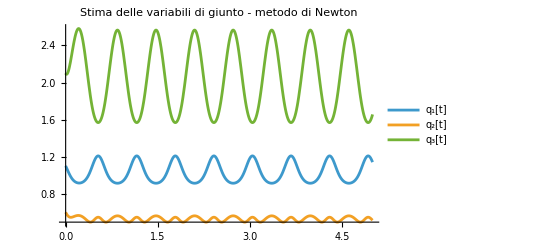

-Graphics-

```mathematica
res=osservatore[{xx3,yy3,zz3},{x3,y3,z3},t,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]},{Subscript[q, 1,i],Subscript[q, 2,i],Subscript[q, 3,i]},tf, "1",λ,μ, "Stima delle variabili di giunto - metodo di Newton","Traiettoria ideale e reale end effector - metodo di Newton"];
res[[1]]
res[[2]]
```

### Metodo del gradiente

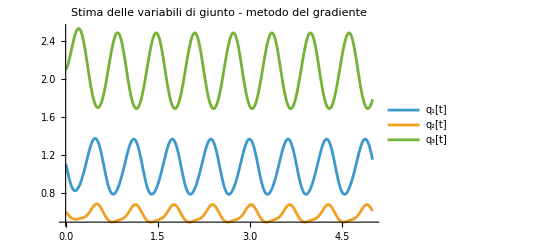

-Graphics-

```mathematica
res=osservatore[{xx3,yy3,zz3},{x3,y3,z3},t,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]},{Subscript[q, 1,i],Subscript[q, 2,i],Subscript[q, 3,i]},tf, "2",λ,μ, "Stima delle variabili di giunto - metodo del gradiente","Traiettoria ideale e reale end effector - metodo del gradiente"];
res[[1]]
res[[2]]
```

### Metodo misto

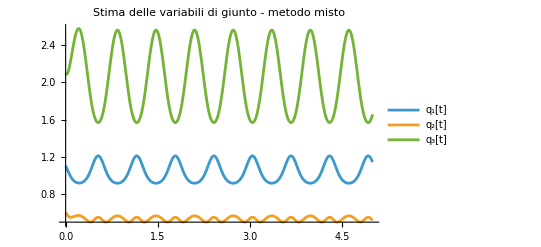

-Graphics-

```mathematica
res=osservatore[{xx3,yy3,zz3},{x3,y3,z3},t,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]},{Subscript[q, 1,i],Subscript[q, 2,i],Subscript[q, 3,i]},tf, "3",λ,μ, "Stima delle variabili di giunto - metodo misto","Traiettoria ideale e reale end effector - metodo misto"];
res[[1]]
res[[2]]
```

## Energia cinetica

```mathematica
xyz={{0,Subscript[L, 1]/2,0},{0,-Subscript[L, 2]/2,0},{0,0,-Subscript[L, 3]/2}};
tab2=Join[tab,xyz,2];
TableForm[tab2,TableHeadings->{{"1","2","3"},{"θ","d","α","a","x","y","z"}}]
```

| θ | d | α | a | x | y | z
1 | q_1 | L_1 | -π/2 | 0 | 0 | L_1/2 | 0
2 | q_2 | L_2 | π/2 | 0 | 0 | -L_2/2 | 0
3 | 0 | q_3 | 0 | 0 | 0 | 0 | -L_3/2

```mathematica
{T,U}=energiaRobot[tab2,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]}];
```

Link1

B_ω  (I_(1y) | 0 | 0
0 | 0 | 0
0 | 0 | 0)

B_t  (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

B  (I_(1y) | 0 | 0
0 | 0 | 0
0 | 0 | 0)

T_1  1/2 I_(1y) (q_1')^2

T_2  0

T  1/2 I_(1y) (q_1')^2

U  4.905 m_1 L_1

Link2

B_ω  (c_2^2 I_(2z)+I_(2x) s_2^2 | 0 | 0
0 | I_(2y) | 0
0 | 0 | 0)

B_t  (1/4 m_2 L_2^2 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

B  (c_2^2 I_(2z)+I_(2x) s_2^2+1/4 m_2 L_2^2 | 0 | 0
0 | I_(2y) | 0
0 | 0 | 0)

T_1  1/2 ((c_2^2 I_(2z)+I_(2x) s_2^2) (q_1')^2+I_(2y) (q_2')^2)

T_2  1/8 m_2 L_2^2 (q_1')^2

T  1/8 ((4 c_2^2 I_(2z)+4 I_(2x) s_2^2+m_2 L_2^2) (q_1')^2+4 I_(2y) (q_2')^2)

U  9.81 m_2 L_1

Link3

B_ω  (c_2^2 I_(3z)+I_(3x) s_2^2 | 0 | 0
0 | I_(3y) | 0
0 | 0 | 0)

B_t  (1/4 m_3 (4 L_2^2+s_2^2 (L_3-2 q_3)^2) | 1/2 c_2 m_3 L_2 (L_3-2 q_3) | -m_3 s_2 L_2
1/2 c_2 m_3 L_2 (L_3-2 q_3) | 1/4 m_3 (L_3-2 q_3)^2 | 0
-m_3 s_2 L_2 | 0 | m_3)

B  (c_2^2 I_(3z)+m_3 L_2^2+1/4 s_2^2 (4 I_(3x)+m_3 (L_3-2 q_3)^2) | 1/2 c_2 m_3 L_2 (L_3-2 q_3) | -m_3 s_2 L_2
1/2 c_2 m_3 L_2 (L_3-2 q_3) | I_(3y)+1/4 m_3 (L_3-2 q_3)^2 | 0
-m_3 s_2 L_2 | 0 | m_3)

T_1  1/2 ((c_2^2 I_(3z)+I_(3x) s_2^2) (q_1')^2+I_(3y) (q_2')^2)

T_2  1/8 m_3 (4 L_2^2 (q_1')^2+(L_3-2 q_3)^2 (s_2^2 (q_1')^2+(q_2')^2)+4 (q_3')^2+4 L_2 q_1' (c_2 (L_3-2 q_3) q_2'-2 s_2 q_3'))

T  1/8 (4 ((c_2^2 I_(3z)+I_(3x) s_2^2) (q_1')^2+I_(3y) (q_2')^2)+m_3 (4 L_2^2 (q_1')^2+(L_3-2 q_3)^2 (s_2^2 (q_1')^2+(q_2')^2)+4 (q_3')^2+4 L_2 q_1' (c_2 (L_3-2 q_3) q_2'-2 s_2 q_3')))

U  9.81 m_3 (L_1-1/2 c_2 (L_3-2 q_3))

Risultati

Energia cinetica totale  1/8 ((4 (I_(1y)+c_2^2 I_(2z)+I_(2x) s_2^2)+m_2 L_2^2) (q_1')^2+4 I_(2y) (q_2')^2+4 ((c_2^2 I_(3z)+I_(3x) s_2^2) (q_1')^2+I_(3y) (q_2')^2)+m_3 (4 L_2^2 (q_1')^2+(L_3-2 q_3)^2 (s_2^2 (q_1')^2+(q_2')^2)+4 (q_3')^2+4 L_2 q_1' (c_2 (L_3-2 q_3) q_2'-2 s_2 q_3')))

Energia potenziale gravitazionale totale  (4.905 m_1+9.81 m_2) L_1+9.81 m_3 (L_1-1/2 c_2 (L_3-2 q_3))

## Eulero Lagrange

```mathematica
F=1/2*{Subscript[q, 1]',Subscript[q, 2]',Subscript[q, 3]'}.DiagonalMatrix[{Subscript[f, 1],Subscript[f, 2],Subscript[f, 3]}].{Subscript[q, 1]',Subscript[q, 2]',Subscript[q, 3]'};
euleroLagrange[T,U,F,{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]},{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]}]//TableForm
```

f_1 q_1'+Sin[2 q_2] (I_(2x)-I_(2z)) q_1' q_2'+Sin[2 q_2] (I_(3x)-I_(3z)) q_1' q_2'+(Sin[q_2]^2 I_(3x)+Cos[q_2]^2 I_(3z)) q_1''+1/4 (4 (I_(1y)+Sin[q_2]^2 I_(2x)+Cos[q_2]^2 I_(2z))+m_2 L_2^2) q_1''+1/8 m_3 (2 Sin[2 q_2] (L_3-2 q_3)^2 q_1' q_2'-8 Sin[q_2]^2 (L_3-2 q_3) q_1' q_3'+8 L_2^2 q_1''+2 Sin[q_2]^2 (L_3-2 q_3)^2 q_1''+4 L_2 (-Sin[q_2] (L_3-2 q_3) (q_2')^2-4 Cos[q_2] q_2' q_3'+Cos[q_2] (L_3-2 q_3) q_2''-2 Sin[q_2] q_3''))==u_1
1/8 (Sin[q_2] m_3 (39.24 L_3-78.48 q_3)-Sin[2 q_2] (4 I_(2x)-4 I_(2z)+4 I_(3x)-4 I_(3z)+m_3 (L_3-2 q_3)^2) (q_1')^2+8 q_2' (f_2-m_3 (L_3-2 q_3) q_3')+Cos[q_2] m_3 L_2 (4. L_3-8. q_3) q_1''+2 (4 I_(2y)+4 I_(3y)+m_3 (L_3-2 q_3)^2) q_2'')==u_2
f_3 q_3'+m_3 (9.81 Cos[q_2]+1/2 (L_3-2 q_3) (Sin[q_2]^2 (q_1')^2+(q_2')^2)-Sin[q_2] L_2 q_1''+q_3'')==u_3